```mathematica
l=.5;
k=100;
fdm=Table[Table[0,{j,k}],{i,k}];
For[i=1,i≤k,++i,
For[j=1,j≤k,++j,
If[i==j,
fdm[[i,j]]=1-2*l,
If[j==i-1∨j==i+1,
fdm[[i,j]]=l
];];];];
Table[Table[If[j==i,fdm[[i,j]]=1,fdm[[i,j]]=0],{j,k}],{i,{1,k}}];

u=Table[If[i==1,20,0],{i,k}];
```

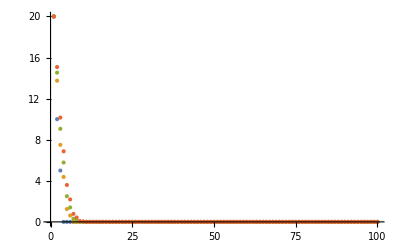

```mathematica
temp={};
ti=u;
For[k=1,k≤10,++k,
ti=fdm.ti;
AppendTo[temp,ti]
];

ListPlot[{temp[[2]],temp[[5]],temp[[7]],temp[[9]]}]
```

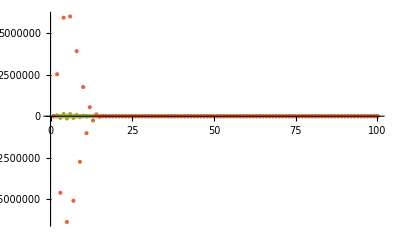

```mathematica
l=2;
k=100;
fdm=Table[Table[0,{j,k}],{i,k}];
For[i=1,i≤k,++i,
For[j=1,j≤k,++j,
If[i==j,
fdm[[i,j]]=1-2*l,
If[j==i-1∨j==i+1,
fdm[[i,j]]=l
];];];];
Table[Table[If[j==i,fdm[[i,j]]=1,fdm[[i,j]]=0],{j,k}],{i,{1,k}}];


temp={};
For[k=1,k≤10,++k,
ti=fdm.ti;
AppendTo[temp,ti]
];

ListPlot[{temp[[2]],temp[[5]],temp[[7]],temp[[9]]}]
```

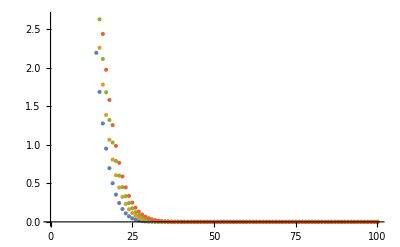

```mathematica
l=2((.001)/(.01));
k=100;
fdm=Table[Table[0,{j,k}],{i,k}];
For[i=1,i≤k,++i,
For[j=1,j≤k,++j,
If[i==j,
fdm[[i,j]]=1-2*l,
If[j==i-1∨j==i+1,
fdm[[i,j]]=l
];];];];
Table[Table[If[j==i,fdm[[i,j]]=1,fdm[[i,j]]=0],{j,k}],{i,{1,k}}];


temp={};
For[k=1,k≤100,++k,
ti=fdm.ti;
AppendTo[temp,ti]
];

ListPlot[{temp[[29]],temp[[59]],temp[[79]],temp[[99]]}]
```